### Estimation parameters

```mathematica
capN=50
m=3
```

50

3

```mathematica
6
```

6

### Recursion for the coefficients of the integer valued polynomials

```mathematica
q[0]:=1;
q[s_]:=Product[x-k,{k,1,s}]/Factorial[s];
```

```mathematica
q[0,0]:=1;
q[0,m_]:=0;
q[s_,k_]:=q[s-1,k-1]/s- q[s-1,k];
```

```mathematica
q[0,0]
q[0,10]
q[0,-1]
q[4,-1]
Table[q[s,k],{s,0,5},{k,0,5}] //MatrixForm
Expand[q[0]]
Expand[q[1]]
Expand[q[2]]
Expand[q[3]]
Expand[q[4]]
Expand[q[5]]
```

1

0

0

0

(1 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0
1 | -3/2 | 1/2 | 0 | 0 | 0
-1 | 11/6 | -1 | 1/6 | 0 | 0
1 | -25/12 | 35/24 | -5/12 | 1/24 | 0
-1 | 137/60 | -15/8 | 17/24 | -1/8 | 1/120)

1

-1+x

1-(3 x)/2+x^2/2

-1+(11 x)/6-x^2+x^3/6

1-(25 x)/12+(35 x^2)/24-(5 x^3)/12+x^4/24

-1+(137 x)/60-(15 x^2)/8+(17 x^3)/24-x^4/8+x^5/120

### Coefficient of the discrete orthogonal polynomials

```mathematica
d[k_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s],{s,0,k}]
P[k_,i_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s,i],{s,0,k}];
```

```mathematica
Table[P[k,i],{k,0,5},{i,0,5}] //MatrixForm
Expand[d[0]]
Expand[d[1]]
Expand[d[2]]
Expand[d[3]]
Expand[d[4]]
Expand[d[5]]
```

(1 | 0 | 0 | 0 | 0 | 0
-51 | 2 | 0 | 0 | 0 | 0
1326 | -153 | 3 | 0 | 0 | 0
-23426 | 15761/3 | -255 | 10/3 | 0 | 0
316251 | -113900 | 117835/12 | -595/2 | 35/12 | 0
-3478761 | 8984502/5 | -947835/4 | 12201 | -1071/4 | 21/10)

1

-51+2 x

1326-153 x+3 x^2

-23426+(15761 x)/3-255 x^2+(10 x^3)/3

316251-113900 x+(117835 x^2)/12-(595 x^3)/2+(35 x^4)/12

-3478761+(8984502 x)/5-(947835 x^2)/4+12201 x^3-(1071 x^4)/4+(21 x^5)/10

### Cramer-Rao bounds

```mathematica
CRB[i_,snr_]:=Sum[P[k,i]^2/Binomial[capN+k,2*k+1]/Binomial[2*k,k],{k,0,m}]/(2*snr);
ApproxCRB[i_,snr_]:=1/(2*capN^(2*i+1)*snr)*(1/(2*i+1)+(m+1)^2/(2*capN*(i+1)^2)-1/(2*capN))*((m+i+1)*Binomial[m+i,i]*Binomial[m,i])^2;
```

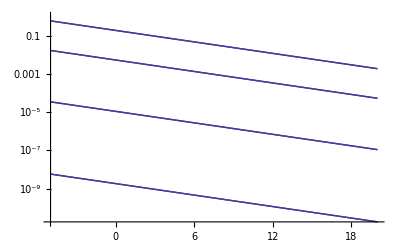

```mathematica
LogPlot[Flatten[Table[{CRB[i,10^(snrdb/10)],ApproxCRB[i,10^(snrdb/10)]},{i,0,m}]],{snrdb,-5,20}]
```

```mathematica
Table[{CRB[2,10^(snrdb/10)],ApproxCRB[2,10^(snrdb/10)]},{snrdb,-5,20}]
```

{{46763/(431600624 √10),1683/(15625000 √10)},{46763/(431600624 10^(3/5)),1683/(15625000 10^(3/5))},{46763/(431600624 10^(7/10)),1683/(15625000 10^(7/10))},{46763/(431600624 10^(4/5)),1683/(15625000 10^(4/5))},{46763/(431600624 10^(9/10)),1683/(15625000 10^(9/10))},{46763/4316006240,1683/156250000},{46763/(4316006240 10^(1/10)),1683/(156250000 10^(1/10))},{46763/(4316006240 10^(1/5)),1683/(156250000 10^(1/5))},{46763/(4316006240 10^(3/10)),1683/(156250000 10^(3/10))},{46763/(4316006240 10^(2/5)),1683/(156250000 10^(2/5))},{46763/(4316006240 √10),1683/(156250000 √10)},{46763/(4316006240 10^(3/5)),1683/(156250000 10^(3/5))},{46763/(4316006240 10^(7/10)),1683/(156250000 10^(7/10))},{46763/(4316006240 10^(4/5)),1683/(156250000 10^(4/5))},{46763/(4316006240 10^(9/10)),1683/(156250000 10^(9/10))},{46763/43160062400,1683/1562500000},{46763/(43160062400 10^(1/10)),1683/(1562500000 10^(1/10))},{46763/(43160062400 10^(1/5)),1683/(1562500000 10^(1/5))},{46763/(43160062400 10^(3/10)),1683/(1562500000 10^(3/10))},{46763/(43160062400 10^(2/5)),1683/(1562500000 10^(2/5))},{46763/(43160062400 √10),1683/(1562500000 √10)},{46763/(43160062400 10^(3/5)),1683/(1562500000 10^(3/5))},{46763/(43160062400 10^(7/10)),1683/(1562500000 10^(7/10))},{46763/(43160062400 10^(4/5)),1683/(1562500000 10^(4/5))},{46763/(43160062400 10^(9/10)),1683/(1562500000 10^(9/10))},{46763/431600624000,1683/15625000000}}

Plot the CRBs to a file

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/crbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[CRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m3i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m3i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/crbN50m3i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[ApproxCRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m3i0".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m3i1".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "/home/mckillrg/Software/polynomialphasecrbs/code/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN50m3i2".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

```mathematica
FullSimplify[Factorial[s+k]/Factorial[s]/Factorial[k]*Factorial[n-s-1]/Factorial[n-k-1]/Factorial[n-k+s]*Binomial[l+k,l]*Binomial[n-l-1,N-k-1]/Binomial[2*k,k]/Binomial[n+k,2*k+1]]
```

((1+2 k) Binomial[k+l,l] Binomial[-1-l+n,-1-k+N] (k+s)! Gamma[1+k] Gamma[n-s])/(Gamma[1+k+n] Gamma[1+s] Gamma[1-k+n+s])

```mathematica
FullSimplify[Binomial[n-s-1,n-k-1]/Binomial[n+k,2*k+1]]
```

Binomial[-1+n-s,-1-k+n]/Binomial[k+n,1+2 k]

```mathematica
StirlingS1[
```